# Лабораторная работа №7

## Грицак Александра, ПО-4

### 1. Элементарная описательная статистика

```mathematica
data = RandomInteger[{0,100},20]
```

{4,13,20,24,42,7,30,62,88,69,33,34,18,20,52,40,36,30,29,17}

```mathematica
Mean[data](*вычисление срелнее арифметическое значение элементов списка*)
```

167/5

```mathematica
Median[data](*нахождение медианы(срединное значение) элементов в списке, т.е. значение находящееся в середине этого набора *)
```

30

```mathematica
Variance[data] (*возвращает дисперсию элементов (дисперсия это мера того, насколько далеко набор чисел отличается от их среднего значения )*)
```

42554/95

```mathematica
Covariance[data](*ковариация  - мера того как две случайные величины изменяются при сравнении друг с другом*)
```

42554/95

```mathematica
Min[data]
```

4

```mathematica
Max[data]
```

88

```mathematica
MinMax[data]
```

{4,88}

```mathematica
StandardDeviation[data] (*квадратный корень из дисперсии (мера разброса числовых данных)*)
```

√(42554/95)

```mathematica
Sort[data]
```

{4,7,13,17,18,20,20,24,29,30,30,33,34,36,40,42,52,62,69,88}

```mathematica
Quantile[data,1/2] (*дает квантиль опред. уровня списка значений , квантиль - значение , которое заданная случайная величина не привышает с фикисрованной вероятностью , (в примере 0,5 квантиль (вторая квартиль))*)
```

30

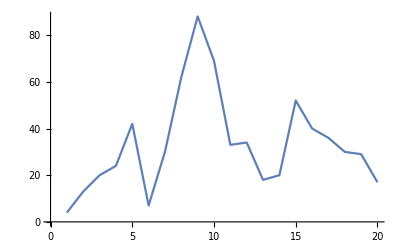

```mathematica
ListLinePlot[data]
```

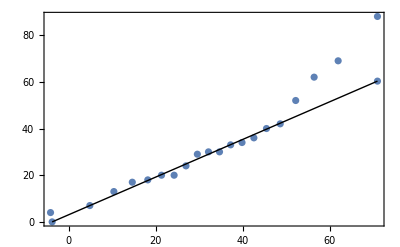

```mathematica
QuantilePlot[data]
```

### 2. Выполнение линейной регрессии

```mathematica
data={{4,2},{3,0},{3,2},{3,4},{2,2},{1,6},{5,2}};model=LinearModelFit[data,x,x]
(*Воспользуемся функцией LinearModelFit для создания линейной модели для заданного набора данных:*)
```

FittedModel[4.97143-0.8 x]

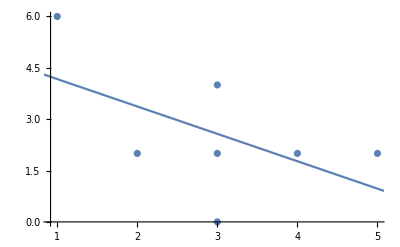

```mathematica
Show[ListPlot[data], Plot[model[x], {x, 0, 20}]]
(*Отобразим данные и линию наилучшего соответствия:*)
```

```mathematica
model["FitResiduals"] (*выведем наблюдаемые остатки а также изобразим их на графике*)
```

{0.228571,-2.57143,-0.571429,1.42857,-1.37143,1.82857,1.02857}

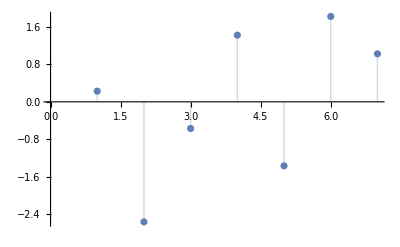

```mathematica
ListPlot[model["FitResiduals"], Filling->Axis]
```

```mathematica
model["StandardizedResiduals"] (*выведем стандартизированные остатки а также изобразим их на графике*)
```

{0.150096,-1.58703,-0.352673,0.881682,-0.900577,1.54533,0.869251}

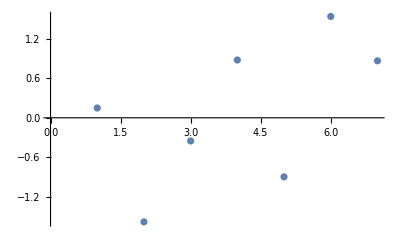

```mathematica
ListPlot[model["StandardizedResiduals"]]
```

```mathematica
model["ParameterTable"] (*Получим информацию по оценке параметров выполненной регрессии:*)
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 4.97143 | 1.78721 | 2.78167 | 0.0388254
x | -0.8 | 0.553431 | -1.44553 | 0.207936

### 3. Замена или удаление недостающих или недействительных данных

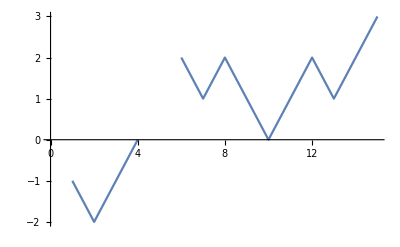

```mathematica
data={-1,-2,-1,0,Missing[],2,1,2,1,0,1,2,1,2,3};
ListLinePlot[data]
```

```mathematica
DeleteMissing[data]
```

{-1,-2,-1,0,2,1,2,1,0,1,2,1,2,3}

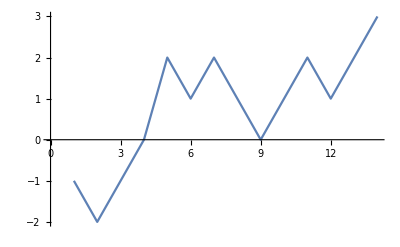

```mathematica
ListLinePlot[%]
```

```mathematica
ElementData[100,"ThermalConductivity"] (*пытаемся вывести теплопроводность 100-го элемента*)
```

Missing[NotAvailable]

```mathematica
data =ElementData[#,"SoundSpeed"]&/@ElementData[]
```

{1270. m/s,970. m/s,6000. m/s,13000. m/s,16200. m/s,18350. m/s,333.6 m/s,317.5 m/s,Missing[NotAvailable],936. m/s,3200. m/s,4602. m/s,5100. m/s,2200. m/s,Missing[NotAvailable],Missing[NotAvailable],206. m/s,319. m/s,2000. m/s,3810. m/s,Missing[NotAvailable],4140. m/s,4560. m/s,5940. m/s,5150. m/s,4910. m/s,4720. m/s,4970. m/s,3570. m/s,3700. m/s,2740. m/s,5400. m/s,Missing[NotAvailable],3350. m/s,Missing[NotAvailable],1120. m/s,1300. m/s,Missing[NotAvailable],3300. m/s,3800. m/s,3480. m/s,6190. m/s,Missing[NotAvailable],5970. m/s,4700. m/s,3070. m/s,2600. m/s,2310. m/s,1215. m/s,2500. m/s,3420. m/s,2610. m/s,Missing[NotAvailable],1090. m/s,Missing[NotAvailable],1620. m/s,2475. m/s,2100. m/s,2280. m/s,2330. m/s,Missing[NotAvailable],2130. m/s,Missing[NotAvailable],2680. m/s,2620. m/s,2710. m/s,2760. m/s,2830. m/s,Missing[NotAvailable],1590. m/s,Missing[Unknown],3010. m/s,3400. m/s,5174. m/s,4700. m/s,4940. m/s,4825. m/s,2680. m/s,1740. m/s,1407. m/s,818. m/s,1260. m/s,1790. m/s,Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],2490. m/s,Missing[Unknown],3155. m/s,Missing[Unknown],2260. m/s,Missing[Unknown],Missing[Unknown],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[Unknown],Missing[NotAvailable],Missing[NotAvailable],Missing[Unknown],Missing[NotAvailable],Missing[NotAvailable],Missing[Unknown],Missing[NotAvailable],Missing[NotAvailable]}

```mathematica
data2 = Take[data,10]
```

{1270. m/s,970. m/s,6000. m/s,13000. m/s,16200. m/s,18350. m/s,333.6 m/s,317.5 m/s,Missing[NotAvailable],936. m/s}

```mathematica
SynthesizeMissingValues[data2]
```

{1270. m/s,970. m/s,6000. m/s,13000. m/s,16200. m/s,18350. m/s,333.6 m/s,317.5 m/s,329.769 m/s,936. m/s}

### 4. Выполнение операций с подгруппами данных

```mathematica
ddata={{nowork,67,2},{work,48,3},{nowork,33,1},{work,76,2},{work,33,3},{work,40,6},{nowork,78,1},{nowork,54,3},{work,46,5},{work,36,2},{work,69,1},{nowork,75,3},{nowork,77,2},{work,79,2},{nowork,45,4},{nowork,36,1},{work,58,3},{work,25,1},{nowork,75,3},{work,22,2},{work,51,2},{work,27,6},{work,47,1},{work,69,3},{nowork,52,2}};
(*набор данных *)
```

```mathematica
GatherBy[ddata,First]  (*групируем по статусу (рабоает/безработный)*)
```

{{{nowork,67,2},{nowork,33,1},{nowork,78,1},{nowork,54,3},{nowork,75,3},{nowork,77,2},{nowork,45,4},{nowork,36,1},{nowork,75,3},{nowork,52,2}},{{work,48,3},{work,76,2},{work,33,3},{work,40,6},{work,46,5},{work,36,2},{work,69,1},{work,79,2},{work,58,3},{work,25,1},{work,22,2},{work,51,2},{work,27,6},{work,47,1},{work,69,3}}}

```mathematica
TakeList[ddata, {2}](*первые два подмножества*)
```

{{{nowork,67,2},{work,48,3}}}

```mathematica
SortBy[ddata,#⟦2⟧&] (*сортировка по возрасту*)
```

{{work,22,2},{work,25,1},{work,27,6},{nowork,33,1},{work,33,3},{nowork,36,1},{work,36,2},{work,40,6},{nowork,45,4},{work,46,5},{work,47,1},{work,48,3},{work,51,2},{nowork,52,2},{nowork,54,3},{work,58,3},{nowork,67,2},{work,69,1},{work,69,3},{nowork,75,3},{nowork,75,3},{work,76,2},{nowork,77,2},{nowork,78,1},{work,79,2}}

```mathematica
DeleteDuplicatesBy[ddata, #[[2]]&] (*удалить дубликаты по возрасту*)
```

{{nowork,67,2},{work,48,3},{nowork,33,1},{work,76,2},{work,40,6},{nowork,78,1},{nowork,54,3},{work,46,5},{work,36,2},{work,69,1},{nowork,75,3},{nowork,77,2},{work,79,2},{nowork,45,4},{work,58,3},{work,25,1},{work,22,2},{work,51,2},{work,27,6},{work,47,1},{nowork,52,2}}

```mathematica
Union[ddata](*только уникальные подмножества*)
```

{{nowork,33,1},{nowork,36,1},{nowork,45,4},{nowork,52,2},{nowork,54,3},{nowork,67,2},{nowork,75,3},{nowork,77,2},{nowork,78,1},{work,22,2},{work,25,1},{work,27,6},{work,33,3},{work,36,2},{work,40,6},{work,46,5},{work,47,1},{work,48,3},{work,51,2},{work,58,3},{work,69,1},{work,69,3},{work,76,2},{work,79,2}}